### DMRG ⟨σσ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{0.6319967765174531,0.48857715985398276,0.4389694564183839,0.4068674461684058,0.38490307923708506,0.36804948915813773,0.3549127962952205,0.34421083732363467,0.3354457859814165,0.3281218922228694,0.32201021438733124,0.3168744551810463,0.3125946504591138,0.3090442867441435,0.306156877003633,0.30386097173698334,0.3021205855040111,0.30089617541077623,0.30017216869167634,0.2999304743017528}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

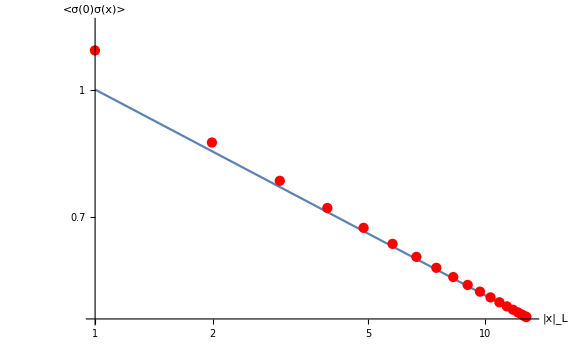

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp2, PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
√(((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528)
```

1.32854

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/plots

```mathematica
Export["fig-sigma-sigma.pdf",g]
```

fig-sigma-sigma.pdf

### DMRG ⟨ϵϵ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],((L/π)Sin[20 π/L])^-2/0.0014561975206714428{0.21036470881938163,0.10380767427270507,0.05828720083840144,0.01953085890256981,0.011722953664760671,0.007745839371092772,0.005711886789146192,0.0044059234222894594,0.0035721543520163546,0.002980672364247927,0.0025638868545783955,0.00225201963193139,0.002021572756812834,0.0018451766607710807,0.0017134080794678208,0.001613788879077288,0.0015425862960726233,0.0014935649314098964,0.0014657867406172587,0.0014561975206714428}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

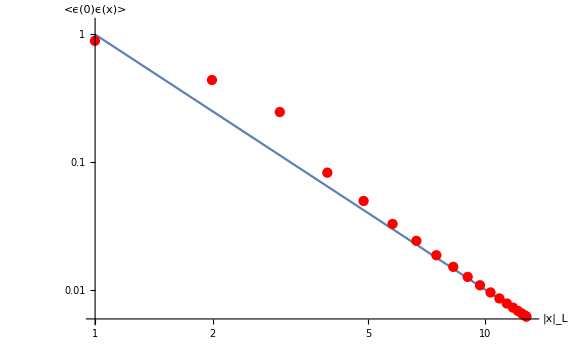

```mathematica
g=Show[LogLogPlot[1/y^2,{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp2, PlotStyle->Red],AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
√(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)
```

2.05816

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/plots

```mathematica
Export["fig-eps-eps.pdf",g]
```

fig-eps-eps.pdf

### DMRG ⟨σσϵ⟩

```mathematica
data$temp=Abs/@{0.12437853107744494, -0.10918628313480952, 0.10380758320196523, -0.10437485622633542, 0.10181807304395053, -0.10023129144748673, 0.09827489616527886, -0.09682192706784315, 0.095382787505695, -0.09426830682280679, 0.0932482893590145, -0.09246478827778926, 0.09179446036934762, -0.09131266592769169, 0.09094914413849978, -0.09074816663718277, 0.09066974634279802, -0.0907419551749113, 0.09094481112578084, -0.09129745426804425, 0.09179554197773128, -0.09245344575569024, 0.09328168280439571, -0.09429314343979764, 0.09551578857094681, -0.09696508908969237, 0.09869372404563323, -0.10072752928921519, 0.10316043330404945, -0.10604840303557848, 0.10956610717780911, -0.1138625901028327, 0.11930337537172636, -0.12639319219383255, 0.1361106885025227, -0.15108371441060794, 0.17633364136277443, -0.2655927392616145, 0.3174038878073508, -0.10918628313480952, 0.05368380312369995, -0.05003900112383972, 0.058196557280829425, -0.06097218962568935, 0.06200030167124257, -0.06221074131816348, 0.06220765501055796, -0.0620170429597612, 0.06183813062734937, -0.06163419726389891, 0.0614929970119651, -0.06138264322374346, 0.061348712116679124, -0.06137012059037291, 0.061473485053079806, -0.06164707852415924, 0.061907952463085274, -0.06225260283778644, 0.06269306642446311, -0.06323397519598374, 0.06388503324873043, -0.06466017015835071, 0.06556907768023622, -0.06663827395118226, 0.06788055343582813, -0.06934212916272522, 0.07104507287173266, -0.07307077725657692, 0.07546621713227043, -0.07838546361382054, 0.08194961957552897, -0.08649291484424608, 0.09241399897047382, -0.10064931316794126, 0.11323109688401985, -0.13505220665577994, 0.20721616027994505, -0.2654537152211821, 0.10380758320196523, -0.05003900112383972, 0.010921369204204261, -0.014408179894977132, 0.01953111684573793, -0.02212185930126251, 0.023655338035249815, -0.02461200855475964, 0.025278069429279505, -0.02576071915659709, 0.026143197338265887, -0.02646301476280229, 0.026751885617137573, -0.02702661166862991, 0.02730208396104019, -0.02758790746263175, 0.027892648502799218, -0.02822347058305118, 0.028586738946455276, -0.028989544867270713, 0.02943823699281524, -0.029941449589369895, 0.03050707116919091, -0.031147374616196755, 0.03187363154262569, -0.03270524904130402, 0.03366015254383807, -0.034772090576570436, 0.03607266780673995, -0.037627425048389083, 0.03949903839463207, -0.041835934093411485, 0.044785745380695886, -0.048775423108706674, 0.054267492865111434, -0.0631891993787549, 0.0784177295209785, -0.13513895680107355, 0.17630767889893129, -0.10437485622633542, 0.058196557280829425, -0.014408179894977132, 0.0070382116416591, -0.008371906108199852, 0.011717511291539131, -0.013726423846409047, 0.01499988669421198, -0.01590477113396483, 0.01657863229060795, -0.017113681479994133, 0.017559056502730472, -0.017948363478002844, 0.018304131133250807, -0.018641685589571428, 0.018973596262692172, -0.0193085503184748, 0.01965512425805105, -0.020019609197160185, 0.02040943382737178, -0.020830729330849618, 0.0212914792607498, -0.021799231827864987, 0.022364475147984595, -0.02299790266540195, 0.023715531594850514, -0.02453424646106054, 0.025481678607986977, -0.026587484577939594, 0.027905719699897323, -0.02949476230641273, 0.03147877591654947, -0.033994523246569916, 0.037405337161162885, -0.04213584945031968, 0.04985964066081792, -0.0631825256136794, 0.11330422270626014, -0.1510440029523342, 0.10181807304395053, -0.06097218962568935, 0.01953111684573793, -0.008371906108199852, 0.003906260879489259, -0.005365413656318449, 0.007745902725498392, -0.00931200225724946, 0.010400669990622865, -0.01121203539733762, 0.011854430249760314, -0.01238358430556789, 0.012840823681979065, -0.013249313245797008, 0.013628492912111986, -0.013990638626506922, 0.014346653053088824, -0.014704756220942227, 0.015072337328902305, -0.01545648689620039, 0.01586354156544692, -0.016301242156415905, 0.016776513220546428, -0.017299659290085492, 0.017879785595689167, -0.01853269369983353, 0.01927228939708939, -0.020125738217889662, 0.02111736854509122, -0.022299962858934843, 0.02372184276925393, -0.025503050814966132, 0.02775901248886508, -0.030837044242181467, 0.03510367214360072, -0.04214173711789027, 0.054267416935425285, -0.10072825263044033, 0.13607806897120778, -0.10023129144748673, 0.06200030167124257, -0.02212185930126251, 0.011717511291539131, -0.005365413656318449, 0.002951684247381624, -0.0038389522213922536, 0.005710544418828136, -0.006995515943984852, 0.007923827731260309, -0.008651884445996533, 0.009244915027438069, -0.009751572019219622, 0.010198401825294166, -0.010606915359542697, 0.010990891292766269, -0.011361987362108557, 0.01172912565523304, -0.012100037837429144, 0.012481990535333653, -0.012881393961069132, 0.013305822306277736, -0.013762093577791916, 0.01425994164202952, -0.01480820862980175, 0.015421549597119295, -0.016113370228903714, 0.01690870532889214, -0.0178308998524431, 0.0189286487675993, -0.020248162404519463, 0.021900622668209125, -0.02399615986456191, 0.026858102400991943, -0.0308351115441791, 0.03740905256089979, -0.04877314084886849, 0.09248884257943617, -0.12635585517957837, 0.09827489616527886, -0.06221074131816348, 0.023655338035249815, -0.013726423846409047, 0.007745902725498392, -0.0038389522213922536, 0.0020766609233634423, -0.0029379812002525486, 0.004405938598625727, -0.005480929436619662, 0.0062931080574906775, -0.0069485666321694945, 0.007500634334318161, -0.007982247301862071, 0.008417086378266448, -0.008820694043679146, 0.009205801176326951, -0.009581910721079313, 0.009957270515000657, -0.010339328523698496, 0.010734634813121964, -0.011150774375606732, 0.011594359771707134, -0.01207500910615684, 0.012601005066866094, -0.013186718204926055, 0.01384449069675231, -0.014598748756378808, 0.015470864270581215, -0.016508184666841653, 0.017753127977037403, -0.01931343790503545, 0.02129087305215428, -0.023997702551273887, 0.027758771357294886, -0.03399992740537294, 0.04478536667883414, -0.0865693595706268, 0.11926750625918617, -0.09682192706784315, 0.06220765501055796, -0.02461200855475964, 0.01499988669421198, -0.00931200225724946, 0.005710544418828136, -0.0029379812002525486, 0.001702323475866355, -0.0023217681772175693, 0.003571624555604575, -0.004499138049176363, 0.005220526640479816, -0.005820221388556789, 0.006335867362866932, -0.006796355484367114, 0.007218895220866229, -0.007617770469101838, 0.008003184060162408, -0.008383997206787308, 0.008767907847953487, -0.009161724709258046, 0.009573020348392415, -0.010008442056743108, 0.010477348842082713, -0.010987914493996115, 0.011553927284805246, -0.012187455168310286, 0.012911809748808428, -0.013747747042970548, 0.01474042730391466, -0.015930958844506994, 0.01742227701433817, -0.01931278802986929, 0.02190156024008527, -0.02550233333240302, 0.031483621007207946, -0.04183483505156585, 0.08202398316637546, -0.1138240084269639, 0.095382787505695, -0.0620170429597612, 0.025278069429279505, -0.01590477113396483, 0.010400669990622865, -0.006995515943984852, 0.004405938598625727, -0.0023217681772175693, 0.0013387147690281027, -0.0019354240008297244, 0.0029806837930386105, -0.0037965862264452903, 0.004448759694202347, -0.005003086411671488, 0.005490696657753977, -0.0059336445278211965, 0.0063472206575724555, -0.006743107895969009, 0.007130636036557492, -0.00751805916786385, 0.007912359276746902, -0.008321309793617978, 0.008751506607029403, -0.009212302870464352, 0.009711620226459874, -0.010263057880252195, 0.010878165698006925, -0.011579799538716438, 0.012387692594547493, -0.01334598339214291, 0.014493782502621195, -0.01593152368407467, 0.017753024458419014, -0.020249690854914088, 0.023721869435316196, -0.029500419908508473, 0.03949883618103863, -0.07846045447204063, 0.10952796697192424, -0.09426830682280679, 0.06183813062734937, -0.02576071915659709, 0.01657863229060795, -0.01121203539733762, 0.007923827731260309, -0.005480929436619662, 0.003571624555604575, -0.0019354240008297244, 0.001158279101953886, -0.001629393629231744, 0.0025636400196057257, -0.003296058828304489, 0.003895464259491337, -0.0044155192196652475, 0.004881111060162838, -0.005311499146885288, 0.005719323763630256, -0.0061151505896943695, 0.006507637105067808, -0.006904259931656359, 0.007312899497261543, -0.007740334536379418, 0.008195811775230388, -0.008687264355201419, 0.00922795335298734, -0.009829292014983627, 0.010513458387008288, -0.01129978587426195, 0.012231046981208478, -0.013345475768569684, 0.014740471496502422, -0.016507528382959897, 0.01892964963779064, -0.02229956158774037, 0.027910972032232202, -0.037626789262413904, 0.07554012373861167, -0.10600867754054302, 0.0932482893590145, -0.06163419726389891, 0.026143197338265887, -0.017113681479994133, 0.011854430249760314, -0.008651884445996533, 0.0062931080574906775, -0.004499138049176363, 0.0029806837930386105, -0.001629393629231744, 0.0009743675490514727, -0.0014324475249051405, 0.0022520493353726046, -0.00292115591336019, 0.0034795489741653823, -0.003973295365750276, 0.004423094836740308, -0.004845365695902821, 0.00525126674128418, -0.005650651694973449, 0.006051260432450605, -0.006461454281755354, 0.006888072260049458, -0.007340503288033706, 0.007826573247351752, -0.008359471113325335, 0.00895031839994229, -0.009620996499009542, 0.010390226530659963, -0.011300048807031943, 0.012387473785421736, -0.013748087425694274, 0.015470485228098739, -0.017832191068443123, 0.021117341196274415, -0.026593155718033726, 0.03607250691833067, -0.07314500797051428, 0.10312078625424392, -0.09246478827778926, 0.0614929970119651, -0.02646301476280229, 0.017559056502730472, -0.01238358430556789, 0.009244915027438069, -0.0069485666321694945, 0.005220526640479816, -0.0037965862264452903, 0.0025636400196057257, -0.0014324475249051405, 0.0008776505310481593, -0.0012633097650256635, 0.0020214534814966337, -0.002642038778761192, 0.003170460249356446, -0.0036453088006546323, 0.004084857492624822, -0.004503500320223887, 0.00491172296534753, -0.005318293075640293, 0.005731791644683043, -0.006159499681094192, 0.006610831481383056, -0.007093748417818875, 0.007621271090203295, -0.008204472398882088, 0.008864818097489515, -0.009620773374642837, 0.010513483830158423, -0.011579343921846492, 0.012911892221643767, -0.014598075685208685, 0.01690966966521232, -0.02012541750844121, 0.025487080989517713, -0.03477167890451078, 0.07111871862632164, -0.10068692093719846, 0.09179446036934762, -0.06138264322374346, 0.026751885617137573, -0.017948363478002844, 0.012840823681979065, -0.009751572019219622, 0.007500634334318161, -0.005820221388556789, 0.004448759694202347, -0.003296058828304489, 0.0022520493353726046, -0.0012633097650256635, 0.0007739777508179832, -0.0011535165935412102, 0.001845187774577111, -0.002429938238293148, 0.0029357977656468727, -0.003398117729453536, 0.003832366083847861, -0.00425216544987936, 0.004666716782923664, -0.005085551121403886, 0.005516115902485702, -0.0059682400832558775, 0.006449880444224002, -0.0069741558589142254, 0.007551970720156466, -0.008204649437437265, 0.008950276656928522, -0.00982949711294168, 0.010877910251533084, -0.012187738498565063, 0.013844000591885957, -0.01611448851646724, 0.019272130611573526, -0.024539845177089313, 0.03366004242384831, -0.06941606771931502, 0.0986531887056776, -0.09131266592769169, 0.061348712116679124, -0.02702661166862991, 0.018304131133250807, -0.013249313245797008, 0.010198401825294166, -0.007982247301862071, 0.006335867362866932, -0.005003086411671488, 0.003895464259491337, -0.00292115591336019, 0.0020214534814966337, -0.0011535165935412102, 0.0007202673276319112, -0.0010562706858839447, 0.001713336685461053, -0.0022713603309577495, 0.0027627223202815517, -0.0032181258645652393, 0.003652455713201408, -0.0040777493337766915, 0.004503977745502406, -0.004939484860661068, 0.005394218073146268, -0.0058765132195865806, 0.006399449487351709, -0.006974022497832829, 0.007621315160299176, -0.008359295174889071, 0.00922801348844683, -0.010262665435997239, 0.011554066306689507, -0.013186061452261777, 0.015422458448147889, -0.018532294645034093, 0.02372087982874011, -0.032704929583073625, 0.06795411985130648, -0.09692390771855827, 0.09094914413849978, -0.06137012059037291, 0.02730208396104019, -0.018641685589571428, 0.013628492912111986, -0.010606915359542697, 0.008417086378266448, -0.006796355484367114, 0.005490696657753977, -0.0044155192196652475, 0.0034795489741653823, -0.002642038778761192, 0.001845187774577111, -0.0010562706858839447, 0.0006586901211014923, -0.000993353029598117, 0.0016137912787249022, -0.002154024268761958, 0.002636542664889881, -0.0030908481461256096, 0.0035298674196032795, -0.0039663006941977694, 0.004408863412030344, -0.004868317126709147, 0.005353103521046325, -0.005876639661564643, 0.006449871727146181, -0.0070939195317234255, 0.007826527133942666, -0.008687454866905147, 0.009711386084998087, -0.010988227287408387, 0.012600523602041188, -0.014809269210080835, 0.017879501941196696, -0.02300335721934169, 0.031873482606154746, -0.06671202078317917, 0.0954746341344328, -0.09074816663718277, 0.061473485053079806, -0.02758790746263175, 0.018973596262692172, -0.013990638626506922, 0.010990891292766269, -0.008820694043679146, 0.007218895220866229, -0.0059336445278211965, 0.004881111060162838, -0.003973295365750276, 0.003170460249356446, -0.002429938238293148, 0.001713336685461053, -0.000993353029598117, 0.0006305383936876785, -0.0009398187421961749, 0.0015425440932291762, -0.0020717444683551025, 0.002552108196672093, -0.0030103564695293885, 0.0034600385436566908, -0.003912499292131159, 0.00437881519865306, -0.004868253050986406, 0.005394269592161103, -0.00596815749441721, 0.00661093971070274, -0.007340400281191091, 0.008195941159729233, -0.009212018111617221, 0.010477613370726392, -0.012074473002288293, 0.014260915807436965, -0.017299237820576657, 0.022369759097822538, -0.031147086433409545, 0.06564260964518115, -0.09425160978378797, 0.09066974634279802, -0.06164707852415924, 0.027892648502799218, -0.0193085503184748, 0.014346653053088824, -0.011361987362108557, 0.009205801176326951, -0.007617770469101838, 0.0063472206575724555, -0.005311499146885288, 0.004423094836740308, -0.0036453088006546323, 0.0029357977656468727, -0.0022713603309577495, 0.0016137912787249022, -0.0009398187421961749, 0.0005943263436559954, -0.0009060567376375034, 0.0014935630889729818, -0.0020189586025214585, 0.002502500358517132, -0.0029709439108676237, 0.0034364484570156536, -0.003912563375328003, 0.0044088920245210165, -0.0049396188052650055, 0.005516122004368793, -0.006159720714204591, 0.006888098698832472, -0.007740599479066477, 0.008751375584147089, -0.010008864812884263, 0.011593983990040213, -0.013763207381116194, 0.016776176868746755, -0.02180456938693968, 0.030506884453553075, -0.06473384827307074, 0.09324021498830103, -0.0907419551749113, 0.061907952463085274, -0.02822347058305118, 0.01965512425805105, -0.014704756220942227, 0.01172912565523304, -0.009581910721079313, 0.008003184060162408, -0.006743107895969009, 0.005719323763630256, -0.004845365695902821, 0.004084857492624822, -0.003398117729453536, 0.0027627223202815517, -0.002154024268761958, 0.0015425440932291762, -0.0009060567376375034, 0.0005838983973645637, -0.0008833439002719895, 0.0014657724396027663, -0.0019935510675876673, 0.0024868427769091607, -0.0029709925510652928, 0.003460096805609905, -0.003966317493693505, 0.004504051853435175, -0.005085493537165277, 0.005731962768171657, -0.00646145566455873, 0.007313153353460843, -0.008321176592174843, 0.009573437551724575, -0.011150391231804049, 0.013306907943322954, -0.01630082904041207, 0.021296697062517248, -0.029941163152444526, 0.06395859667952766, -0.0924117994540811, 0.09094481112578084, -0.06225260283778644, 0.028586738946455276, -0.020019609197160185, 0.015072337328902305, -0.012100037837429144, 0.009957270515000657, -0.008383997206787308, 0.007130636036557492, -0.0061151505896943695, 0.00525126674128418, -0.004503500320223887, 0.003832366083847861, -0.0032181258645652393, 0.002636542664889881, -0.0020717444683551025, 0.0014935630889729818, -0.0008833439002719895, 0.000565242067869787, -0.000870879987385652, 0.0014561943702519852, -0.0019933333002551228, 0.0025025231644632356, -0.003010388852196621, 0.0035299125830241776, -0.004077853715626598, 0.004666719155065224, -0.005318514110418718, 0.006051330550330961, -0.006904611368144266, 0.007912335689592804, -0.009162255811906297, 0.01073438073756891, -0.012882600527346987, 0.015863203806391443, -0.02083598100013564, 0.02943800855042297, -0.06330764896799507, 0.09175399646295189, -0.09129745426804425, 0.06269306642446311, -0.028989544867270713, 0.02040943382737178, -0.01545648689620039, 0.012481990535333653, -0.010339328523698496, 0.008767907847953487, -0.00751805916786385, 0.006507637105067808, -0.005650651694973449, 0.00491172296534753, -0.00425216544987936, 0.003652455713201408, -0.0030908481461256096, 0.002552108196672093, -0.0020189586025214585, 0.0014657724396027663, -0.000870879987385652, 0.0005694481007038228, -0.0008738300109510114, 0.001465790727495051, -0.002019222388583661, 0.0025521911191569054, -0.003090947040396156, 0.0036525785131889233, -0.004252181081086831, 0.004911886107881879, -0.005650658441048596, 0.006507950492232851, -0.007518018722430395, 0.008768430139387228, -0.010339083034453874, 0.012483204855338445, -0.015456119757032465, 0.020414607221736773, -0.0289892448721138, 0.06276667696787556, -0.09125587974365683, 0.09179554197773128, -0.06323397519598374, 0.02943823699281524, -0.020830729330849618, 0.01586354156544692, -0.012881393961069132, 0.010734634813121964, -0.009161724709258046, 0.007912359276746902, -0.006904259931656359, 0.006051260432450605, -0.005318293075640293, 0.004666716782923664, -0.0040777493337766915, 0.0035298674196032795, -0.0030103564695293885, 0.002502500358517132, -0.0019935510675876673, 0.0014561943702519852, -0.0008738300109510114, 0.000565146003751223, -0.0008803874150715809, 0.0014935862337403182, -0.00207158931391813, 0.002636604397120422, -0.0032182197540517894, 0.0038324068399614207, -0.0045036624287361025, 0.005251299016258708, -0.006115508326554085, 0.0071306503542914405, -0.008384583100771342, 0.009957118236238748, -0.012101366426203256, 0.01507207989338311, -0.020024863906914814, 0.028586521775160308, -0.06232632610577242, 0.09090340657930908, -0.09245344575569024, 0.06388503324873043, -0.029941449589369895, 0.0212914792607498, -0.016301242156415905, 0.013305822306277736, -0.011150774375606732, 0.009573020348392415, -0.008321309793617978, 0.007312899497261543, -0.006461454281755354, 0.005731791644683043, -0.005085551121403886, 0.004503977745502406, -0.0039663006941977694, 0.0034600385436566908, -0.0029709439108676237, 0.0024868427769091607, -0.0019933333002551228, 0.001465790727495051, -0.0008803874150715809, 0.000584105913209245, -0.0009090773522883722, 0.0015426088601773456, -0.002154312888809208, 0.0027628405964553746, -0.0033981915923946052, 0.0040850031072430905, -0.004845368865342057, 0.005719614923894325, -0.006743055475994822, 0.008003706920027194, -0.009581724842866379, 0.011730430213748337, -0.014704459423624174, 0.01966031516893511, -0.028223191796976226, 0.061981648180876134, -0.09070065270575756, 0.09328168280439571, -0.06466017015835071, 0.03050707116919091, -0.021799231827864987, 0.016776513220546428, -0.013762093577791916, 0.011594359771707134, -0.010008442056743108, 0.008751506607029403, -0.007740334536379418, 0.006888072260049458, -0.006159499681094192, 0.005516115902485702, -0.004939484860661068, 0.004408863412030344, -0.003912499292131159, 0.0034364484570156536, -0.0029709925510652928, 0.0025025231644632356, -0.002019222388583661, 0.0014935862337403182, -0.0009090773522883722, 0.0005940189750097115, -0.0009367804726919839, 0.0016138062660331516, -0.0022711985901542105, 0.0029358104106274275, -0.0036454128559104356, 0.004423101000204862, -0.005311755905091947, 0.006347148339990267, -0.007618289297865326, 0.00920564756868717, -0.011363344669002795, 0.014346440041058693, -0.01931383396290702, 0.027892471778804273, -0.061720906329468965, 0.09062868565990775, -0.09429314343979764, 0.06556907768023622, -0.031147374616196755, 0.022364475147984595, -0.017299659290085492, 0.01425994164202952, -0.01207500910615684, 0.010477348842082713, -0.009212302870464352, 0.008195811775230388, -0.007340503288033706, 0.006610831481383056, -0.0059682400832558775, 0.005394218073146268, -0.004868317126709147, 0.00437881519865306, -0.003912563375328003, 0.003460096805609905, -0.003010388852196621, 0.0025521911191569054, -0.00207158931391813, 0.0015426088601773456, -0.0009367804726919839, 0.0006309952145692488, -0.0009965153744734803, 0.001713402180019065, -0.002430184610493042, 0.0031705878151358654, -0.003973328509818201, 0.0048813072700921, -0.0059334867197117945, 0.007219303282553923, -0.00882045298576287, 0.010992169811473086, -0.01399036423814436, 0.018978834041736132, -0.027587683767487423, 0.061547333597931596, -0.09070737901823124, 0.09551578857094681, -0.06663827395118226, 0.03187363154262569, -0.02299790266540195, 0.017879785595689167, -0.01480820862980175, 0.012601005066866094, -0.010987914493996115, 0.009711620226459874, -0.008687264355201419, 0.007826573247351752, -0.007093748417818875, 0.006449880444224002, -0.0058765132195865806, 0.005353103521046325, -0.004868253050986406, 0.0044088920245210165, -0.003966317493693505, 0.0035299125830241776, -0.003090947040396156, 0.002636604397120422, -0.002154312888809208, 0.0016138062660331516, -0.0009965153744734803, 0.0006581126700623028, -0.0010530273792449612, 0.001845143828739322, -0.0026418625390856524, 0.0034795125802098924, -0.004415648513623594, 0.0054905271071942555, -0.0067967401629746675, 0.008416873375606338, -0.010608235030032448, 0.01362825280895208, -0.018646956932853186, 0.027301901593253013, -0.06144406788171027, 0.09090866980309822, -0.09696508908969237, 0.06788055343582813, -0.03270524904130402, 0.023715531594850514, -0.01853269369983353, 0.015421549597119295, -0.013186718204926055, 0.011553927284805246, -0.010263057880252195, 0.00922795335298734, -0.008359471113325335, 0.007621271090203295, -0.0069741558589142254, 0.006399449487351709, -0.005876639661564643, 0.005394269592161103, -0.0049396188052650055, 0.004504051853435175, -0.004077853715626598, 0.0036525785131889233, -0.0032182197540517894, 0.0027628405964553746, -0.0022711985901542105, 0.001713402180019065, -0.0010530273792449612, 0.0007210154126281004, -0.0011568940771774603, 0.0020215301202918872, -0.00292138014144698, 0.003895614666147822, -0.005002938947902579, 0.006336195103317052, -0.007982009777849873, 0.010199691203532119, -0.01324901677540226, 0.018309325859074313, -0.027026330266255134, 0.06142269713154509, -0.09127265067395966, 0.09869372404563323, -0.06934212916272522, 0.03366015254383807, -0.02453424646106054, 0.01927228939708939, -0.016113370228903714, 0.01384449069675231, -0.012187455168310286, 0.010878165698006925, -0.009829292014983627, 0.00895031839994229, -0.008204472398882088, 0.007551970720156466, -0.006974022497832829, 0.006449871727146181, -0.00596815749441721, 0.005516122004368793, -0.005085493537165277, 0.004666719155065224, -0.004252181081086831, 0.0038324068399614207, -0.0033981915923946052, 0.0029358104106274275, -0.002430184610493042, 0.001845143828739322, -0.0011568940771774603, 0.0007730236345801562, -0.0012597722146841359, 0.002251986864379078, -0.003295908006370711, 0.004448571327158242, -0.0058205047206002355, 0.007500448368775415, -0.009752916862363755, 0.012840580865357002, -0.017953593996571416, 0.026751576944292338, -0.06145665548671041, 0.09175482494578834, -0.10072752928921519, 0.07104507287173266, -0.034772090576570436, 0.025481678607986977, -0.020125738217889662, 0.01690870532889214, -0.014598748756378808, 0.012911809748808428, -0.011579799538716438, 0.010513458387008288, -0.009620996499009542, 0.008864818097489515, -0.008204649437437265, 0.007621315160299176, -0.0070939195317234255, 0.00661093971070274, -0.006159720714204591, 0.005731962768171657, -0.005318514110418718, 0.004911886107881879, -0.0045036624287361025, 0.0040850031072430905, -0.0036454128559104356, 0.0031705878151358654, -0.0026418625390856524, 0.0020215301202918872, -0.0012597722146841359, 0.0008788648854634949, -0.0014362156323652767, 0.0025637608969795974, -0.003796702024169813, 0.005220861012860175, -0.0069484325614776535, 0.009246235116064242, -0.012383306928464136, 0.01756419774033759, -0.026462583340733196, 0.06156708972754618, -0.09242584259877125, 0.10316043330404945, -0.07307077725657692, 0.03607266780673995, -0.026587484577939594, 0.02111736854509122, -0.0178308998524431, 0.015470864270581215, -0.013747747042970548, 0.012387692594547493, -0.01129978587426195, 0.010390226530659963, -0.009620773374642837, 0.008950276656928522, -0.008359295174889071, 0.007826527133942666, -0.007340400281191091, 0.006888098698832472, -0.00646145566455873, 0.006051330550330961, -0.005650658441048596, 0.005251299016258708, -0.004845368865342057, 0.004423101000204862, -0.003973328509818201, 0.0034795125802098924, -0.00292138014144698, 0.002251986864379078, -0.0014362156323652767, 0.0009728628947755516, -0.0016253812986176453, 0.0029805124691149776, -0.004499161393078905, 0.006292960359876659, -0.008653189497472895, 0.01185421893876057, -0.017118871207737713, 0.02614274402396015, -0.0617084081991366, 0.09320996180683262, -0.10604840303557848, 0.07546621713227043, -0.037627425048389083, 0.027905719699897323, -0.022299962858934843, 0.0189286487675993, -0.016508184666841653, 0.01474042730391466, -0.01334598339214291, 0.012231046981208478, -0.011300048807031943, 0.010513483830158423, -0.00982949711294168, 0.00922801348844683, -0.008687454866905147, 0.008195941159729233, -0.007740599479066477, 0.007313153353460843, -0.006904611368144266, 0.006507950492232851, -0.006115508326554085, 0.005719614923894325, -0.005311755905091947, 0.0048813072700921, -0.004415648513623594, 0.003895614666147822, -0.003295908006370711, 0.0025637608969795974, -0.0016253812986176453, 0.0011601687549058607, -0.0019396873458827292, 0.0035718520691751035, -0.0054810310410208524, 0.007925066432338153, -0.011211783359113612, 0.016583729853815374, -0.025760090046479313, 0.061912521010641874, -0.09423109347360711, 0.10956610717780911, -0.07838546361382054, 0.03949903839463207, -0.02949476230641273, 0.02372184276925393, -0.020248162404519463, 0.017753127977037403, -0.015930958844506994, 0.014493782502621195, -0.013345475768569684, 0.012387473785421736, -0.011579343921846492, 0.010877910251533084, -0.010262665435997239, 0.009711386084998087, -0.009212018111617221, 0.008751375584147089, -0.008321176592174843, 0.007912335689592804, -0.007518018722430395, 0.0071306503542914405, -0.006743055475994822, 0.006347148339990267, -0.0059334867197117945, 0.0054905271071942555, -0.005002938947902579, 0.004448571327158242, -0.003796702024169813, 0.0029805124691149776, -0.0019396873458827292, 0.0013362044507617698, -0.0023170618424805073, 0.004405753962852479, -0.006996435979645677, 0.010400446204865844, -0.015909891731701223, 0.025277449670978426, -0.06209171312659625, 0.09534654927561484, -0.1138625901028327, 0.08194961957552897, -0.041835934093411485, 0.03147877591654947, -0.025503050814966132, 0.021900622668209125, -0.01931343790503545, 0.01742227701433817, -0.01593152368407467, 0.014740471496502422, -0.013748087425694274, 0.012911892221643767, -0.012187738498565063, 0.011554066306689507, -0.010988227287408387, 0.010477613370726392, -0.010008864812884263, 0.009573437551724575, -0.009162255811906297, 0.008768430139387228, -0.008384583100771342, 0.008003706920027194, -0.007618289297865326, 0.007219303282553923, -0.0067967401629746675, 0.006336195103317052, -0.0058205047206002355, 0.005220861012860175, -0.004499161393078905, 0.0035718520691751035, -0.0023170618424805073, 0.001705471889426862, -0.00294319842712827, 0.005711626287811613, -0.009311980436574413, 0.01500480776971385, -0.024611146994416157, 0.062282678166165124, -0.0967875123254349, 0.11930337537172636, -0.08649291484424608, 0.044785745380695886, -0.033994523246569916, 0.02775901248886508, -0.02399615986456191, 0.02129087305215428, -0.01931278802986929, 0.017753024458419014, -0.016507528382959897, 0.015470485228098739, -0.014598075685208685, 0.013844000591885957, -0.013186061452261777, 0.012600523602041188, -0.012074473002288293, 0.011593983990040213, -0.011150391231804049, 0.01073438073756891, -0.010339083034453874, 0.009957118236238748, -0.009581724842866379, 0.00920564756868717, -0.00882045298576287, 0.008416873375606338, -0.007982009777849873, 0.007500448368775415, -0.0069484325614776535, 0.006292960359876659, -0.0054810310410208524, 0.004405753962852479, -0.00294319842712827, 0.002072557714297241, -0.0038338959315446478, 0.007745843742329832, -0.013731243098218996, 0.023654758615877534, -0.06228668810223054, 0.09824259329678742, -0.12639319219383255, 0.09241399897047382, -0.048775423108706674, 0.037405337161162885, -0.030837044242181467, 0.026858102400991943, -0.023997702551273887, 0.02190156024008527, -0.020249690854914088, 0.01892964963779064, -0.017832191068443123, 0.01690966966521232, -0.01611448851646724, 0.015422458448147889, -0.014809269210080835, 0.014260915807436965, -0.013763207381116194, 0.013306907943322954, -0.012882600527346987, 0.012483204855338445, -0.012101366426203256, 0.011730430213748337, -0.011363344669002795, 0.010992169811473086, -0.010608235030032448, 0.010199691203532119, -0.009752916862363755, 0.009246235116064242, -0.008653189497472895, 0.007925066432338153, -0.006996435979645677, 0.005711626287811613, -0.0038338959315446478, 0.0029581316417624523, -0.00537204596827945, 0.011721957786139787, -0.02212087178959834, 0.062076529181751064, -0.10020203044069065, 0.1361106885025227, -0.10064931316794126, 0.054267492865111434, -0.04213584945031968, 0.03510367214360072, -0.0308351115441791, 0.027758771357294886, -0.02550233333240302, 0.023721869435316196, -0.02229956158774037, 0.021117341196274415, -0.02012541750844121, 0.019272130611573526, -0.018532294645034093, 0.017879501941196696, -0.017299237820576657, 0.016776176868746755, -0.01630082904041207, 0.015863203806391443, -0.015456119757032465, 0.01507207989338311, -0.014704459423624174, 0.014346440041058693, -0.01399036423814436, 0.01362825280895208, -0.01324901677540226, 0.012840580865357002, -0.012383306928464136, 0.01185421893876057, -0.011211783359113612, 0.010400446204865844, -0.009311980436574413, 0.007745843742329832, -0.00537204596827945, 0.0038977669834704726, -0.008367979110496885, 0.019530270151111515, -0.06104943800829664, 0.10179243849700523, -0.15108371441060794, 0.11323109688401985, -0.0631891993787549, 0.04985964066081792, -0.04214173711789027, 0.03740905256089979, -0.03399992740537294, 0.031483621007207946, -0.029500419908508473, 0.027910972032232202, -0.026593155718033726, 0.025487080989517713, -0.024539845177089313, 0.02372087982874011, -0.02300335721934169, 0.022369759097822538, -0.02180456938693968, 0.021296697062517248, -0.02083598100013564, 0.020414607221736773, -0.020024863906914814, 0.01966031516893511, -0.01931383396290702, 0.018978834041736132, -0.018646956932853186, 0.018309325859074313, -0.017953593996571416, 0.01756419774033759, -0.017118871207737713, 0.016583729853815374, -0.015909891731701223, 0.01500480776971385, -0.013731243098218996, 0.011721957786139787, -0.008367979110496885, 0.0070548691466420805, -0.01441498813295833, 0.05827325132933943, -0.10435759195665767, 0.17633364136277443, -0.13505220665577994, 0.0784177295209785, -0.0631825256136794, 0.054267416935425285, -0.04877314084886849, 0.04478536667883414, -0.04183483505156585, 0.03949883618103863, -0.037626789262413904, 0.03607250691833067, -0.03477167890451078, 0.03366004242384831, -0.032704929583073625, 0.031873482606154746, -0.031147086433409545, 0.030506884453553075, -0.029941163152444526, 0.02943800855042297, -0.0289892448721138, 0.028586521775160308, -0.028223191796976226, 0.027892471778804273, -0.027587683767487423, 0.027301901593253013, -0.027026330266255134, 0.026751576944292338, -0.026462583340733196, 0.02614274402396015, -0.025760090046479313, 0.025277449670978426, -0.024611146994416157, 0.023654758615877534, -0.02212087178959834, 0.019530270151111515, -0.01441498813295833, 0.010895064557839609, -0.050108045749638244, 0.10380709850275646, -0.2655927392616145, 0.20721616027994505, -0.13513895680107355, 0.11330422270626014, -0.10072825263044033, 0.09248884257943617, -0.0865693595706268, 0.08202398316637546, -0.07846045447204063, 0.07554012373861167, -0.07314500797051428, 0.07111871862632164, -0.06941606771931502, 0.06795411985130648, -0.06671202078317917, 0.06564260964518115, -0.06473384827307074, 0.06395859667952766, -0.06330764896799507, 0.06276667696787556, -0.06232632610577242, 0.061981648180876134, -0.061720906329468965, 0.061547333597931596, -0.06144406788171027, 0.06142269713154509, -0.06145665548671041, 0.06156708972754618, -0.0617084081991366, 0.061912521010641874, -0.06209171312659625, 0.062282678166165124, -0.06228668810223054, 0.062076529181751064, -0.06104943800829664, 0.05827325132933943, -0.050108045749638244, 0.05383114056899224, -0.10925129414082262, 0.3174038878073508, -0.2654537152211821, 0.17630767889893129, -0.1510440029523342, 0.13607806897120778, -0.12635585517957837, 0.11926750625918617, -0.1138240084269639, 0.10952796697192424, -0.10600867754054302, 0.10312078625424392, -0.10068692093719846, 0.0986531887056776, -0.09692390771855827, 0.0954746341344328, -0.09425160978378797, 0.09324021498830103, -0.0924117994540811, 0.09175399646295189, -0.09125587974365683, 0.09090340657930908, -0.09070065270575756, 0.09062868565990775, -0.09070737901823124, 0.09090866980309822, -0.09127265067395966, 0.09175482494578834, -0.09242584259877125, 0.09320996180683262, -0.09423109347360711, 0.09534654927561484, -0.0967875123254349, 0.09824259329678742, -0.10020203044069065, 0.10179243849700523, -0.10435759195665767, 0.10380709850275646, -0.10925129414082262, 0.12437857821874772};
data$temp=Riffle[Table[{i,j},{i,2,40},{j,2,40}]//Flatten[#,1]&,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)data$temp]//Partition[#,2]&;
data=Flatten/@data$temp;
```

```mathematica
Ising3pt[x1_,x2_,x3_]:=c123/((Abs[(L/π)Sin[(x1-x2) π/L]])^Δϵ(Abs[(L/π)Sin[(x1-x3) π/L]])^Δϵ(Abs[(L/π)Sin[(x2-x3) π/L]])^(2Δσ-Δϵ))/.{Δϵ->1,Δσ->1/8,c123->1/2};
```

```mathematica
Select[data,#[[1]]==11&];
g1={#[[2]],#[[3]]}&/@%//ListPlot[#,PlotStyle->Red]&;
```

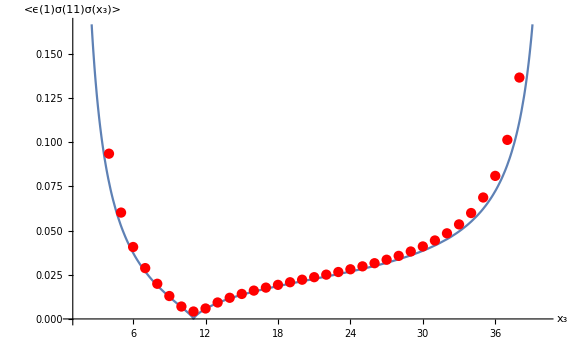

```mathematica
Show[Plot[Ising3pt[1,11,x3],{x3,1,40}],g1,AxesLabel->{"x_3","<ϵ(1)σ(11)σ(x_3)>"},ImageSize->Large,AxesStyle->Large]
```

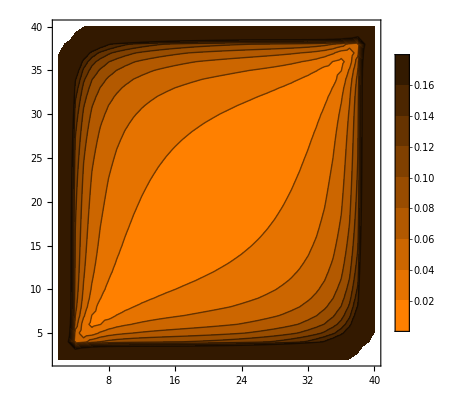

```mathematica
ListContourPlot[data,Contours->{0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16},PlotLegends->Automatic,ContourShading->Table[Darker[Orange,i],{i,0,1,0.1}]]
```

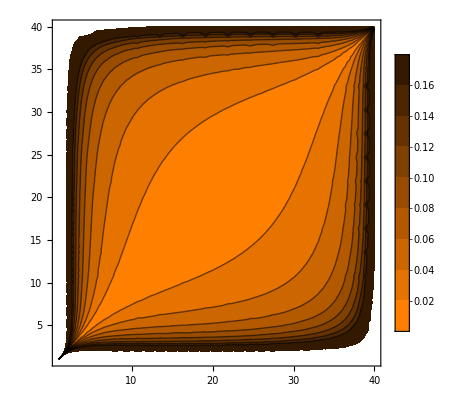

```mathematica
ContourPlot[Ising3pt[1,x2,x3],{x2,1,40},{x3,1,40},Contours->{0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16},PlotLegends->Automatic,ContourShading->Table[Darker[Orange,i],{i,0,1,0.1}]]
```